# Задание 05.

## Базис Грёбнера

## Мосейков Игнатий Геннадьевич, 21372

## 1. Доказательство математических теорем

### Задача

Воспользуйтесь базисом Грёбнера для получения связи между длинами сторон треугольника l_1,l_2,l_3, радиусом описанной окружности R и площадью треугольника S.

### Указания

Удобно завести переменные для положения трех точек (углов треугольника) в виде списков координат, p1 = {x1, y1}; ...,  и положение центра описанной окружности p = {x, y}

Выпишите три полиномиальных соотношения (т.е. уравнения могут содержать положительные степени переменных, но не содержат корней), которые связывают длины сторон l1, l2, l3 и координаты углов треугольника (удобно использовать скалярное произведение Dot для записи теоремы косинусов)

Выпишите три соотношения, которые определяют положение центра описанной окружности (расстояние от точки центра до всех углов должно равняться R — радиусу описанной окружности, можно воспользоваться встроенной функцией EuclideanDistance)

Выпишите одно соотношение для площади треугольника, через координаты его углов (удобно использовать векторное произведение Cross).

Постройте базис Грёбнера для этих 7 соотношений относительно переменных {l1, l2, l3, R, S} (порядок важен), исключив все декартовы координаты {x1, x2, ...}, (обратите внимания на разные способы вызова GroebnerBasis).

Найдите среди полученных соотношений формулу Герона (возможно потребуются преобразование результата, чтобы показать что это именно она) и формулу для радиуса описанной окружности через длины сторон и площадь треугольника.

```mathematica
p1={x1,y1,0};
p2={x2,y2,0};
p3={x3,y3,0};
p={x,y,0};
v1=p2-p1;
v2=p3-p2;
v3=p3-p1;
(*l1=v1.v1;
l2=v2.v2;
l3=v3.v3;
v1v2 =(v1×v2).(v1×v2);*)
pp1 = ComplexExpand [ EuclideanDistance[p,p1] ];
pp2 = ComplexExpand[ EuclideanDistance[p,p2] ];
pp3 = ComplexExpand[ EuclideanDistance[p,p3] ];
eqns={
pp1^2-R^2==0,
pp2^2-R^2==0,
pp3^2-R^2==0,
v2.v2+v3.v3-2v2.v3-l1^2==0,
v1.v1+v3.v3-2v1.v3-l2^2==0,
v1.v1+v2.v2-2v1.v2-l3^2==0,
S-0.5*(v1×v2)[[3]]==0
};
gb = GroebnerBasis[eqns,{l1,l2,l3,R,S},{x1,x2,x3,y1,y2,y3,x,y}]
gb[[ Length[gb] ]]-16 S^2//Factor
```

{1. l2^12-2.5 l2^10 l3^2+2.0625 l2^8 l3^4-0.625 l2^6 l3^6+0.0625 l2^4 l3^8+20. l2^8 S^2-16. l2^6 l3^2 S^2+5. l2^4 l3^4 S^2-8. l2^6 R^2 S^2-26. l2^4 l3^2 R^2 S^2-2. l2^2 l3^4 R^2 S^2+64. l2^4 S^4+64. l2^2 R^2 S^4+16. R^4 S^4,0.333333 l2^10 l3^4-0.833333 l2^8 l3^6+0.6875 l2^6 l3^8-0.208333 l2^4 l3^10+0.0208333 l2^2 l3^12+2.37037 l2^10 S^2-5.92593 l2^8 l3^2 S^2+11.5556 l2^6 l3^4 S^2-6.81481 l2^4 l3^6 S^2+1.81481 l2^2 l3^8 S^2-1.18519 l2^8 R^2 S^2+3.55556 l2^6 l3^2 R^2 S^2-6.88889 l2^4 l3^4 R^2 S^2+1. l1^2 l3^6 R^2 S^2-6.14815 l2^2 l3^6 R^2 S^2-1.33333 l3^8 R^2 S^2+47.4074 l2^6 S^4-37.9259 l2^4 l3^2 S^4+33.1852 l2^2 l3^4 S^4-42.6667 l2^4 R^2 S^4+7.11111 l1^2 l3^2 R^2 S^4-33.1852 l2^2 l3^2 R^2 S^4+1.18519 l3^4 R^2 S^4-7.11111 l1^2 R^4 S^4+11.8519 l2^2 R^4 S^4+20.1481 l3^2 R^4 S^4+151.704 l2^2 S^6+75.8519 R^2 S^6,0.166667 l2^10-0.416667 l2^8 l3^2+0.34375 l2^6 l3^4-0.104167 l2^4 l3^6+0.0104167 l2^2 l3^8+3.33333 l2^6 S^2-2.66667 l2^4 l3^2 S^2+0.833333 l2^2 l3^4 S^2+1. l1^2 l2^2 R^2 S^2-1.66667 l2^4 R^2 S^2+0.5 l1^2 l3^2 R^2 S^2-3.66667 l2^2 l3^2 R^2 S^2-0.666667 l3^4 R^2 S^2+10.6667 l2^2 S^4+5.33333 R^2 S^4,0.592593 l2^8-1.77778 l2^6 l3^2+1. l1^2 l2^2 l3^4+1.77778 l2^4 l3^4-0.592593 l2^2 l3^6+7.11111 l1^2 l2^2 S^2+9.48148 l2^4 S^2-9.48148 l2^2 l3^2 S^2+3.55556 l1^2 R^2 S^2-5.92593 l2^2 R^2 S^2-10.0741 l3^2 R^2 S^2,1. l1^2 l2^4-0.333333 l2^6+0.5 l1^2 l2^2 l3^2+0.666667 l2^4 l3^2-0.333333 l2^2 l3^4-5.33333 l2^2 S^2-2.66667 R^2 S^2,1. l1^4-2. l1^2 l2^2+1. l2^4-2. l1^2 l3^2-2. l2^2 l3^2+1. l3^4+16. S^2}

1. (1. l1^4-2. l1^2 l2^2+1. l2^4-2. l1^2 l3^2-2. l2^2 l3^2+1. l3^4-1.24345×10^-14 S^2)

```mathematica
pp=0.5*(l1+l2+l3);
Simplify[pp*(pp-l1)*(pp-l2)*(pp-l3)]
```

0.5 (l1+l2+l3) (-l1+0.5 (l1+l2+l3)) (-l2+0.5 (l1+l2+l3)) (-l3+0.5 (l1+l2+l3))

```mathematica
gb[[Length[gb]-1]]
```

1. l1^2 l2^4-0.333333 l2^6+0.5 l1^2 l2^2 l3^2+0.666667 l2^4 l3^2-0.333333 l2^2 l3^4-5.33333 l2^2 S^2-2.66667 R^2 S^2

## 2. Манипулятор

### Задача

Для описания манипулятора, показанного на рисунке, мы вводим фиксированные длины двух ребер l_1, l_2 и 4 переменные c_i=cos(θ_i), s_i=sin(θ_i), i=1,2 для значений косинусов и синусов углов θ_1, θ_2 (обратите внимание, что второй угол отсчитывается от направления первого).

Задача заключается в том, чтобы по заданному значению положения {a,b} определить, достижимо ли оно, и, если достижимо, то найти значения углов поворота с использованием базиса Грёбнера.

### Указания

В целях упрощения задачи, присвойте длинам ребер конкретные значения l_1=1, l_2=2 (первое плечо манипулятора короче второго).

Выпишите полиномиальные соотношения между значениями c_i косинусов и s_i синусов углов углами поворота, длинами ребер и координатами {a, b}.

Дополните два, полученных выше соотношения, еще двумя тригонометрическими связями c_i^2+s_i^2=1

Получите базис Грёбнера для этих четырех полиномов относительно набора переменных {c_2,s_2,c_1,s_1} (порядок важен!)

Один из полиномов базиса позволит вам определить область, достижимую манипулятором: достижимую область можно получить из уравнения, в которое входит только s_1. Найдите условия на a и b, при которых это уравнение решается. Что это за область?

Как бы выглядела достижимая область, если бы было  l_1=2, l_2=1 (т.е., наоборот, первое плечо манипулятора длиннее второго)?

Используя полученный базис Грёбнера определите последовательно значения s_1,c_1,s_2,c_2 как функции от a и b.

Создайте интерактивное представление модели (c использованием Animate или Manipulate на ваш выбор): меняется положение {a, b}, и отрисовываются положения плеч манипулятора.

```mathematica
Clear[l1,l2,gb,c1,c2,s1,s2];
l1=1;l2=2;
eqns=
{
-a+l1*c1+l2*(c1*c2-s1*s2)==0,
-b+l1*s1+l2*(s1*c2+s2*c1)==0,
c1^2+s1^2-1==0,
c2^2+s2^2-1==0
};
gb = GroebnerBasis[eqns,{c2,s2,c1,s1}]
gb[[1]]
```

{9-10 a^2+a^4-6 b^2+2 a^2 b^2+b^4+12 b s1-4 a^2 b s1-4 b^3 s1+4 a^2 s1^2+4 b^2 s1^2,3-a^2-b^2+2 a c1+2 b s1,7 a-a^3-a b^2+6 c1-2 b^2 c1+2 a b s1+4 b c1 s1-4 a s1^2,-1+c1^2+s1^2,-b c1+a s1+2 s2,5-a^2-b^2+4 c2}

9-10 a^2+a^4-6 b^2+2 a^2 b^2+b^4+12 b s1-4 a^2 b s1-4 b^3 s1+4 a^2 s1^2+4 b^2 s1^2

```mathematica
{{r1= Solve[gb[[1]]==0,{s1}] 
r2= Solve[gb[[1]]==0,{s1}]}, {□}}
```

{{{{(s1→(-3 b+a^2 b+b^3-√(-9 a^2+10 a^4-a^6+10 a^2 b^2-2 a^4 b^2-a^2 b^4))/(2 (a^2+b^2)))^2},{(s1→(-3 b+a^2 b+b^3+√(-9 a^2+10 a^4-a^6+10 a^2 b^2-2 a^4 b^2-a^2 b^4))/(2 (a^2+b^2)))^2}}},{□}}

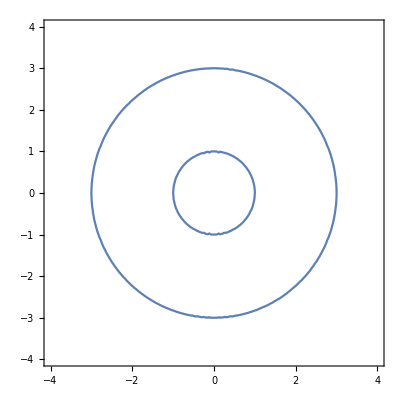

```mathematica
ContourPlot[ {-9 a^2+10 a^4-a^6+10 a^2 b^2-2 a^4 b^2-a^2 b^4== 0}, {a, -4, 4}, {b, -4, 4}]
```

```mathematica
Clear[l1,l2,gb,r1,r2,c1,s1,c2,s2,eqns];
l1=2;l2=1;
eqns=
{
-a+l1*c1+l2*(c1*c2-s1*s2)==0,
-b+l1*s1+l2*(s1*c2+s2*c1)==0,
c1^2+s1^2-1==0,
c2^2+s2^2-1==0
};
gb = GroebnerBasis[eqns,{c2,s2,c1,s1}]
gb[[1]]
r1= Solve[gb[[1]]==0,{s1}] 
r2= Solve[gb[[1]]==0,{s1}]
```

{9-10 a^2+a^4+6 b^2+2 a^2 b^2+b^4-24 b s1-8 a^2 b s1-8 b^3 s1+16 a^2 s1^2+16 b^2 s1^2,-3-a^2-b^2+4 a c1+4 b s1,13 a-a^3-a b^2-12 c1-4 b^2 c1+4 a b s1+16 b c1 s1-16 a s1^2,-1+c1^2+s1^2,-b c1+a s1+s2,5-a^2-b^2+4 c2}

9-10 a^2+a^4+6 b^2+2 a^2 b^2+b^4-24 b s1-8 a^2 b s1-8 b^3 s1+16 a^2 s1^2+16 b^2 s1^2

{{s1→(3 b+a^2 b+b^3-√(-9 a^2+10 a^4-a^6+10 a^2 b^2-2 a^4 b^2-a^2 b^4))/(4 (a^2+b^2))},{s1→(3 b+a^2 b+b^3+√(-9 a^2+10 a^4-a^6+10 a^2 b^2-2 a^4 b^2-a^2 b^4))/(4 (a^2+b^2))}}

{{s1→(3 b+a^2 b+b^3-√(-9 a^2+10 a^4-a^6+10 a^2 b^2-2 a^4 b^2-a^2 b^4))/(4 (a^2+b^2))},{s1→(3 b+a^2 b+b^3+√(-9 a^2+10 a^4-a^6+10 a^2 b^2-2 a^4 b^2-a^2 b^4))/(4 (a^2+b^2))}}

```mathematica
s1/.r2
```

{(3 b+a^2 b+b^3-√(-9 a^2+10 a^4-a^6+10 a^2 b^2-2 a^4 b^2-a^2 b^4))/(4 (a^2+b^2)),(3 b+a^2 b+b^3+√(-9 a^2+10 a^4-a^6+10 a^2 b^2-2 a^4 b^2-a^2 b^4))/(4 (a^2+b^2))}

```mathematica
ContourPlot[ { -9 a^2+10 a^4-a^6+10 a^2 b^2-2 a^4 b^2-a^2 b^4== 0}, {a, -4,4}, {b, -4, 4}]
```

-Graphics-

```mathematica
s11[x_,y_]= (Solve[gb[[1]]==0,{s1}] //First)/.{a->x,b->y}
```

{s1→(3 y+x^2 y+y^3-√(-9 x^2+10 x^4-x^6+10 x^2 y^2-2 x^4 y^2-x^2 y^4))/(4 (x^2+y^2))}

```mathematica
s12[x_,y_]=(Solve[gb[[1]]==0,{s1}] //Last )/.{a->x,b->y}
```

{s1→(3 y+x^2 y+y^3+√(-9 x^2+10 x^4-x^6+10 x^2 y^2-2 x^4 y^2-x^2 y^4))/(4 (x^2+y^2))}

```mathematica
s1/.{s1->(3 y+x^2 y+y^3+√(-9 x^2+10 x^4-x^6+10 x^2 y^2-2 x^4 y^2-x^2 y^4))/(4 (x^2+y^2))}
```

(3 y+x^2 y+y^3+√(-9 x^2+10 x^4-x^6+10 x^2 y^2-2 x^4 y^2-x^2 y^4))/(4 (x^2+y^2))

```mathematica
eq1 = gb[[2]] /.{s1->(s1/.s11[a,b])}
```

-3-a^2-b^2+(b (3 b+a^2 b+b^3-√(-9 a^2+10 a^4-a^6+10 a^2 b^2-2 a^4 b^2-a^2 b^4)))/(a^2+b^2)+4 a c1

```mathematica
c11[x_,y_]=(Solve[ eq1==0,{c1}] //First)/.{a->x,b->y}
```

{c1→(3 x^2+x^4+x^2 y^2+y √(-x^2 (9-10 x^2+x^4-10 y^2+2 x^2 y^2+y^4)))/(4 x (x^2+y^2))}

```mathematica
eq2=gb[[2]]/.{s1->(s1/.s12[a,b])}
```

-3-a^2-b^2+(b (3 b+a^2 b+b^3+√(-9 a^2+10 a^4-a^6+10 a^2 b^2-2 a^4 b^2-a^2 b^4)))/(a^2+b^2)+4 a c1

```mathematica
c12[x_,y_]=(Solve[ eq2==0,{c1}] //First)/.{a->x,b->y}
```

{c1→(3 x^2+x^4+x^2 y^2-y √(-x^2 (9-10 x^2+x^4-10 y^2+2 x^2 y^2+y^4)))/(4 x (x^2+y^2))}

```mathematica
c21[x_,y_]=(Solve[gb[[6]]==0,{c2}] //First)/.{a->x,b->y}
```

{c2→1/4 (-5+x^2+y^2)}

```mathematica
eq3=gb[[5]]/.{s1->(s1/.s11[a,b]),c1->(c1/.c11[a,b])}
```

-(b (3 a^2+a^4+a^2 b^2+b √(-a^2 (9-10 a^2+a^4-10 b^2+2 a^2 b^2+b^4))))/(4 a (a^2+b^2))+(a (3 b+a^2 b+b^3-√(-9 a^2+10 a^4-a^6+10 a^2 b^2-2 a^4 b^2-a^2 b^4)))/(4 (a^2+b^2))+s2

```mathematica
s21[x_,y_]=(Solve[eq3==0,{s2}] //First)/.{a->x,b->y}
```

{s2→(√(-x^2 (9-10 x^2+x^4-10 y^2+2 x^2 y^2+y^4)))/(4 x)}

```mathematica
eq4=gb[[5]]/.{s1->(s1/.s12[a,b]),c1->(c1/.c12[a,b])}
```

-(b (3 a^2+a^4+a^2 b^2-b √(-a^2 (9-10 a^2+a^4-10 b^2+2 a^2 b^2+b^4))))/(4 a (a^2+b^2))+(a (3 b+a^2 b+b^3+√(-9 a^2+10 a^4-a^6+10 a^2 b^2-2 a^4 b^2-a^2 b^4)))/(4 (a^2+b^2))+s2

```mathematica
s22[x_,y_]=(Solve[eq4==0,{s2}] //First)/.{a->x,b->y}
```

{s2→-(√(-x^2 (9-10 x^2+x^4-10 y^2+2 x^2 y^2+y^4)))/(4 x)}

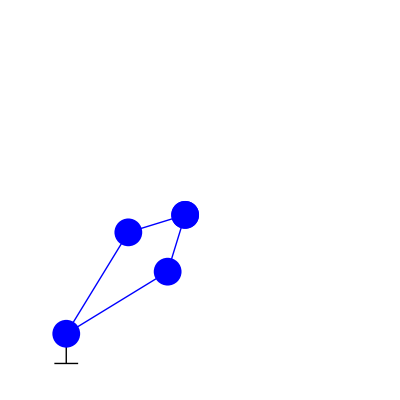

```mathematica
pl[x_,y_]:=Block[{L1,L2,l1,l2,l3,l4,l5,l6,r11x,r11y,r12x,r12y,r21x,r21y,r22x,r22y},
L1=2;L2=1;
r11x=L1*c1/.c11[x,y];
r11y=L1*s1/.s11[x,y];
r21x=L2*( (c2/.c21[x,y])*(c1/.c11[x,y])- (s2/.s21[x,y])*(s1/.s11[x,y]) );
r21y=L2*( (c2/.c21[x,y])* (s1/.s11[x,y])+(c1/.c11[x,y])* (s2/.s21[x,y]));
r12x=L1*c1/.c12[x,y];
r12y=L1*s1/.s12[x,y];
r22x=L2*( (c2/.c21[x,y])*(c1/.c12[x,y])- (s2/.s22[x,y])*(s1/.s12[x,y]) );
r22y=L2*( (c2/.c21[x,y])* (s1/.s12[x,y])+(c1/.c12[x,y])* (s2/.s22[x,y]));
l1=Line[{{-0.2,-0.5},{0.2,-0.5}}];
l2=Line[{{0,-0.5},{0,0}}];
l3=Line[{{0,0},{r11x,r11y},{r11x+r21x,r11y+r21y}}];
l4=Line[{{0,0},{r12x,r12y},{r12x+r22x,r12y+r22y}}];
Graphics[{
{White,Rectangle[{-0.5,-0.5},{5,5}]},
{Thick,l2},
{Thick,l1},
{Thick,Blue,l3},
{Thick,Blue,l4},
{Blue,PointSize[0.05],Point[{0,0}]},
{Blue,PointSize[0.05],Point[{r11x,r11y}]},
{Blue,PointSize[0.05],Point[{r11x+r21x,r11y+r21y}]},
{Blue,PointSize[0.05],Point[{r12x,r12y}]},
{Blue,PointSize[0.05],Point[{r12x+r22x,r12y+r22y}]}

}]
];
pl[2,2]
```

```mathematica
Manipulate[GraphicsRow[{pl[x,y]}],{x,1,3},{y,1,3}]
```